```mathematica
ClearAll["global`*"]
```

```mathematica
χ = Exp[-k*Abs[t]/Subscript[γ, h]]*HeavisideTheta[t]
```

ⅇ^(-(k Abs[t])/γ_h) HeavisideTheta[t]

```mathematica
ⅇ^(-(k Abs[t])/Subscript[γ, h])*HeavisideTheta[t]
```

ⅇ^(-(k Abs[t])/γ_h) HeavisideTheta[t]

```mathematica
Subscript[χ, ω] = Sqrt[2*π]*FullSimplify[FourierTransform[χ,t,ω],Assumptions->{k>0,Subscript[γ, h]>0}]
```

γ_h/(k-ⅈ ω γ_h)

```mathematica
Subscript[R, ω]=Subscript[γ, h]/(-ⅈ*ω*Subscript[γ, h]*Subscript[γ, c]+k*Subscript[γ, h]-k^2*Subscript[χ, ω])
```

γ_h/(k γ_h-ⅈ ω γ_c γ_h-(k^2 γ_h)/(k-ⅈ ω γ_h))

```mathematica
FullSimplify[ComplexExpand[Subscript[R, ω]],Assumptions->{k>0,Subscript[γ, h]>0,Subscript[γ, c]>0,ω∈Reals}]
```

(ⅈ k+ω γ_h)/(ω (k γ_h+γ_c (k-ⅈ ω γ_h)))

```mathematica
rw = ComplexExpand[Subscript[R, ω]]
```

(k γ_h^2)/((k γ_h-(k^3 γ_h)/(k^2+ω^2 γ_h^2))^2+(-ω γ_c γ_h-(k^2 ω γ_h^2)/(k^2+ω^2 γ_h^2))^2)-(k^3 γ_h^2)/((k^2+ω^2 γ_h^2) ((k γ_h-(k^3 γ_h)/(k^2+ω^2 γ_h^2))^2+(-ω γ_c γ_h-(k^2 ω γ_h^2)/(k^2+ω^2 γ_h^2))^2))+ⅈ ((ω γ_c γ_h^2)/((k γ_h-(k^3 γ_h)/(k^2+ω^2 γ_h^2))^2+(-ω γ_c γ_h-(k^2 ω γ_h^2)/(k^2+ω^2 γ_h^2))^2)+(k^2 ω γ_h^3)/((k^2+ω^2 γ_h^2) ((k γ_h-(k^3 γ_h)/(k^2+ω^2 γ_h^2))^2+(-ω γ_c γ_h-(k^2 ω γ_h^2)/(k^2+ω^2 γ_h^2))^2)))

```mathematica
imr = FullSimplify[Im[rw],Assumptions->{k>0,Subscript[γ, h]>0,Subscript[γ, c]>0,ω∈Reals}]
```

(Re[1/ω] (k^2 γ_h+γ_c (k^2+ω^2 γ_h^2)))/(2 k^2 γ_c γ_h+k^2 γ_h^2+γ_c^2 (k^2+ω^2 γ_h^2))

```mathematica
rer = FullSimplify[Re[rw],Assumptions->{k>0,Subscript[γ, h]>0,Subscript[γ, c]>0,ω∈Reals}]
```

(k γ_h^2-Im[1/ω] (k^2 γ_h+γ_c (k^2+ω^2 γ_h^2)))/(2 k^2 γ_c γ_h+k^2 γ_h^2+γ_c^2 (k^2+ω^2 γ_h^2))

```mathematica
FullSimplify[Abs[Subscript[χ, ω]]^2,Assumptions->{k>0,Subscript[γ, h]>0,Subscript[γ, c]>0,ω∈Reals}]
```

γ_h^2/Abs[k-ⅈ ω γ_h]^2

```mathematica
Sxw = FullSimplify[Abs[Subscript[R, ω]]^2*(2*Subscript[γ, c]*Subscript[T, c]+2*k^2*Subscript[T, h]/Subscript[γ, h]*Abs[Subscript[χ, ω]]^2),Assumptions->{k>0,Subscript[γ, h]>0,Subscript[γ, c]>0,ω∈Reals}]
```

(2 (T_c γ_c+(k^2 T_h γ_h)/Abs[k-ⅈ ω γ_h]^2))/(Abs[k-ⅈ ω γ_c-k^2/(k-ⅈ ω γ_h)]^2)

```mathematica
FullSimplify[(Sxw/imr),Assumptions->{k>0,Subscript[γ, h]>0,Subscript[γ, c]>0,ω∈Reals}]
```

(2 (k^2 T_h γ_h+T_c γ_c (k^2+ω^2 γ_h^2)))/(ω (k^2 γ_h+γ_c (k^2+ω^2 γ_h^2)))

```mathematica
FullSimplify[(Sxw/imr)/.{Subscript[T, h]->T,Subscript[T, c]->T},Assumptions->{k>0,Subscript[γ, h]>0,Subscript[γ, c]>0,ω∈Reals}]
```

(2 T)/ω

```mathematica
V= Series[FullSimplify[(Sxw/imr)/.{Subscript[T, c]->T,Subscript[T, h]->T*(1+δ)},Assumptions->{k>0,γ>0,Subscript[γ, c]>0,Subscript[γ, h]>0,ω∈Reals,T>0,-1<δ<1}],{δ,0,10}]
```

Piecewise[{{ComplexInfinity, ω==0}, {(2 T)/ω+(2 k^2 T γ_h δ)/(ω (k^2 γ_c+k^2 γ_h+ω^2 γ_c γ_h^2))+O[δ]^11, True}}]

```mathematica
j = FullSimplify[ComplexExpand[(-ω^2*Sxw-2*Subscript[T, c]*rer)/.{Subscript[T, c]->T,Subscript[T, h]->T*(1+δ)}],Assumptions->{k>0,Subscript[γ, h]>0,Subscript[γ, c]>0,ω∈Reals,T>0,-1<δ<1}]
```

-(2 T (k γ_h (k+k δ+γ_h)+γ_c (k^2+ω^2 γ_h^2)))/(2 k^2 γ_c γ_h+k^2 γ_h^2+γ_c^2 (k^2+ω^2 γ_h^2))

```mathematica
FullSimplify[j/.{δ->0}]
```

-(2 T (k γ_h (k+γ_h)+γ_c (k^2+ω^2 γ_h^2)))/(2 k^2 γ_c γ_h+k^2 γ_h^2+γ_c^2 (k^2+ω^2 γ_h^2))

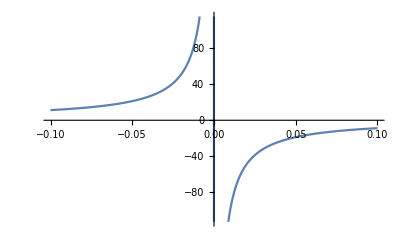

```mathematica
Plot[j/.{k->1,Subscript[γ, h]->1,Subscript[γ, c]->1,T->1,δ->0.5},{ω,-0.1,0.1}]
```

```mathematica
J = Integrate[j,{ω,-∞,∞},Assumptions->{k>0,Subscript[γ, h]>0,Subscript[γ, c]>0,T>0,-1<δ<1}]
```

Integrate[(2 T (k^2 (-1+ω+δ ω) γ_h+(-1+ω) γ_c (k^2+ω^2 γ_h^2)))/(ω (2 k^2 γ_c γ_h+k^2 γ_h^2+γ_c^2 (k^2+ω^2 γ_h^2))),{ω,-∞,∞},Assumptions→{k>0,γ_h>0,γ_c>0,T>0,-1<δ<1}]

```mathematica
Integrate[(2 d k^2 T Subscript[γ, h])/(ω (2 k^2 Subscript[γ, c] Subscript[γ, h]+k^2 Subscript[γ, h]^2+Subscript[γ, c]^2 (k^2+ω^2 Subscript[γ, h]^2))),{ω,-∞,∞},Assumptions->{k>0,Subscript[γ, h]>0,Subscript[γ, c]>0,T>0,-1<δ<1,ω∈Reals}]
```

Integrate[(2 d k^2 T γ_h)/(ω (2 k^2 γ_c γ_h+k^2 γ_h^2+γ_c^2 (k^2+ω^2 γ_h^2))),{ω,-∞,∞},Assumptions→{k>0,γ_h>0,γ_c>0,T>0,-1<δ<1,ω∈Reals}]

```mathematica
sol=Solve[(j)^(-1)==0,ω]
```

{{ω→0},{ω→-(ⅈ k (γ_c+γ_h))/(γ_c γ_h)},{ω→(ⅈ k (γ_c+γ_h))/(γ_c γ_h)}}

```mathematica
om = sol[[3]]
```

{ω→(ⅈ k (γ_c+γ_h))/(γ_c γ_h)}

```mathematica
jf = FullSimplify[j*(ω-(ω/.om))^2]
```

-(2 ⅈ T (k γ_h+γ_c (k+ⅈ ω γ_h)) (k^2 (-1+ω+δ ω) γ_h+(-1+ω) γ_c (k^2+ω^2 γ_h^2)))/(ω γ_c^2 γ_h^2 (ⅈ k γ_h+γ_c (ⅈ k+ω γ_h)))

```mathematica
res = FullSimplify[2*π*(jf/.om)]
```

0